```mathematica
Limit[(1-Exp[-(r/R)^2])^4/r^6,{r->0}, Assumptions->R>0]
```

0

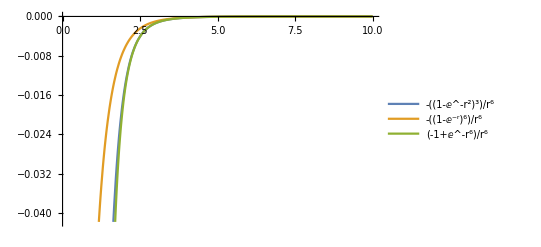

```mathematica
Regulator1[r_,R_]:=-(1-Exp[-(r/R)^2])^3/r^6;
Regulator2[r_,R_]:=-(1-Exp[-(r/R)])^6/r^6;
Regulator3[r_,R_]:=-(1-Exp[-(r/R)^6])/r^6;
Plot[Evaluate@Table[{Regulator1[r,R],Regulator2[r,R], Regulator3[r,R]},{R,1}],{r,0.1,10},PlotLegends->"Expressions"]
```